```mathematica
g[ω_,δ_,ϵ_,m_]:= Inverse[IdentityMatrix[m](ω+ⅈ*δ-ϵ)]
```

```mathematica
lead[ω_,δ_,t_,ϵ_]:=lead[ω,δ,t,ϵ]= Module[{gin= g[ω,δ,ϵ,1],J=g[ω,δ,ϵ,1],T=t*IdentityMatrix[1]},Do[J= Inverse[IdentityMatrix[1]-gin.T.J.T].gin,150000];J=J]
```

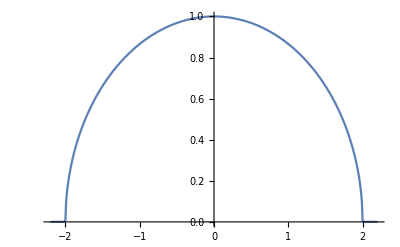

```mathematica
Monitor[ListLinePlot[Table[{ω,-Im[lead[ω,0.0001,1,0]][[1,1]]},{ω,Range[-2.2,2.2,0.01]}]],ω]
```

```mathematica
T[t_]:= t*IdentityMatrix[1]
```

```mathematica
γ[ω_,δ_,t_,ϵ_]:= T[t].lead[ω,δ,t,ϵ].ConjugateTranspose[T[t]]
```

```mathematica
Σ[ω_,δ_,t_,ϵ_]:= -1*Im[lead[ω,δ,t,ϵ]]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)*IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
H[ω_,δ_,t_,ϵ_]:= ReplacePart[β[ω,δ,t,ϵ,100],{{1,1},{100,100}}->ω+ⅈ*δ-lead[ω,δ,t,ϵ][[1,1]]]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
H[0,0.0001,1,0]//MatrixForm
```

```mathematica
f1:= Module[{n= RandomInteger[{1,49}]},{n,n}]
```

```mathematica
f2:= Module[{n= RandomInteger[{51,100}]},{n,n}]
```

```mathematica
list[l_,r_]:=Join[Table[f1,l],Table[f2,r]]
```

```mathematica
dist[l_,r_]:=dist[l,r]= Table[list[l,r],5000]
```

```mathematica
di=dist[5,2][[58]]
```

{{4,4},{2,2},{23,23},{11,11},{24,24},{69,69},{85,85}}

```mathematica
dii={{17,17},{6,6},{10,10},{38,38},{20,20},{63,63},{92,92},{75,75},{57,57}}
```

{{17,17},{6,6},{10,10},{38,38},{20,20},{63,63},{92,92},{75,75},{57,57}}

```mathematica
gpris[w_,d_,t_,e_]:= Inverse[H[w,d,t,e]]
```

```mathematica
Himp[ω_,δ_,t_,ϵ_,ϵ1_,l_,r_,num_]:=ReplacePart[H[ω,δ,t,ϵ],dist[l,r][[num]]->ω-ⅈ*δ-ϵ1]
```

```mathematica
Himp[0,01,1,0,ϵ1,10,10,1]//MatrixForm
```

```mathematica
Gimp[ω_,δ_,t_,ϵ_,l_,r_,num_]:= Inverse[Himp[ω,δ,t,ϵ,0.5,l,r,num]]
```

```mathematica
Monitor[Table[-Im[Gimp[w,0.0001,1,0,5,5,1][[10,10]]],{w,Range[-2.2,2.2,0.01]}],w]//ListLinePlot
```

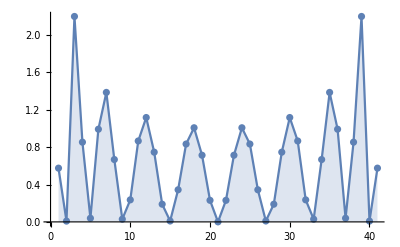

```mathematica
ListPlot[%24,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Monitor[Table[Mean[ParallelTable[-Im[Gimp[w,0.0001,1,0,5,5,N][[10,10]]],{N,50}]],{w,-2,2,0.1}],w]
```

{28.1524,1.24271,1.23124,0.846001,0.71573,0.728595,0.755929,0.594497,0.473636,0.553681,0.640746,0.605037,0.608733,0.508911,0.440116,0.457709,0.587992,0.559979,0.562936,0.404388,0.439756,0.404388,0.562936,0.559979,0.587992,0.457709,0.440116,0.508911,0.608733,0.605037,0.640746,0.553681,0.473636,0.594497,0.755929,0.728595,0.71573,0.846001,1.23124,1.24271,28.1524}

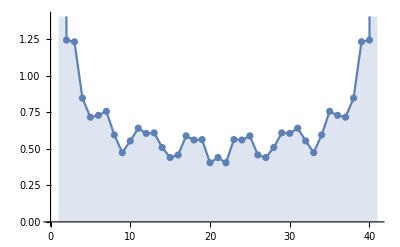

```mathematica
ListPlot[%74,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Monitor[Table[Mean[ParallelTable[-Im[Gimp[w,0.0001,1,0,5,5,N][[10,10]]],{N,5000}]],{w,-2,2,0.1}],w]
```

{0.20882,1.83996,1.2513,1.04387,0.872062,0.738578,0.756403,0.726044,0.611896,0.550381,0.584629,0.579168,0.611171,0.545575,0.492001,0.509009,0.486661,0.559981,0.524591,0.531318,0.489621,0.451688,0.492027,0.500206,0.545124,0.530022,0.53562,0.457238,0.528134,0.560951,0.581732,0.640423,0.595899,0.573707,0.635583,0.769941,0.797937,0.811856,1.1234,1.40656,0.59022}

```mathematica
Mean[ParallelTable[-Im[Gimp[0,0.0001,1,0,0,0,N][[10,10]]],{N,5000}]]
```

0.5

```mathematica
ListLinePlot[Monitor[Table[{w,ParallelTable[-Gimp[w,0.0001,1,0,10,5,N][[10,10]]//Im,{N,2000}]//Mean},{w,Range[-2.2,2.2,0.01]}],w]]
```

$Aborted

```mathematica
Clear[a]
```

```mathematica
a[l_,r_]:=a[l,r]=Table[{w,-Tr[Gimp[w,0.001,1,0,l,r,1]]//Im},{w,Range[-2.2,2.2,0.01]}]
```

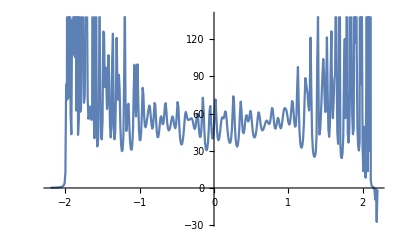

```mathematica
a[10,5]//ListLinePlot
```

```mathematica
Interpolation[a]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[Interpolation[a[5,5]][W],{W,-2.2,2.2}]/(100π)
```

0.951373

```mathematica
G[0,0.0001,1,0,0]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
TRA[ω_,l_,r_,num_]:=4*Tr[Abs[Σ[ω,0.0001,1,0][[1]]*gpris[ω,0.0001,1,0][[1,100]]*Σ[ω,0.0001,1,0][[1]]*Conjugate[gpris[ω,0.0001,1,0][[1,100]]]]]
```

```mathematica
TRA[1,2,4,1]
```

0.988519

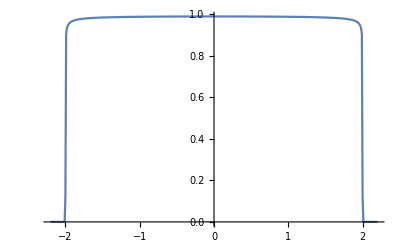

```mathematica
ListLinePlot[Table[{ω,TRA[ω,5,2,1]},{ω,Range[-2.2,2.2,0.01]}],PlotRange->All]
```

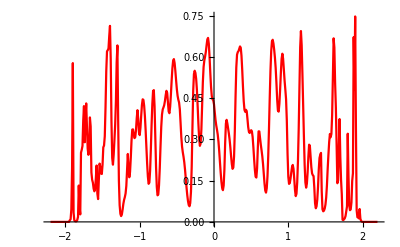

```mathematica
ListLinePlot[Table[{ω,Mean[ParallelTable[TRA[ω,5,2,num],{num,2}]]},{ω,Range[-2.2,2.2,0.01]}],PlotStyle->Red]
```

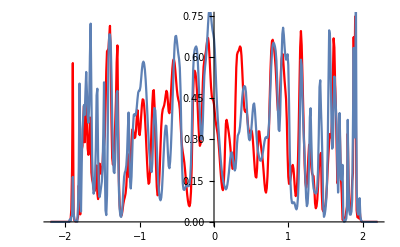

```mathematica
Show[%79,%75]
```

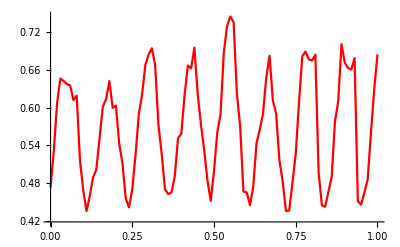

```mathematica
ListLinePlot[Table[{ω,Mean[ParallelTable[TRA[ω,5,4,num],{num,2000}]]},{ω,Range[0,1,0.01]}],PlotStyle->Red]
```

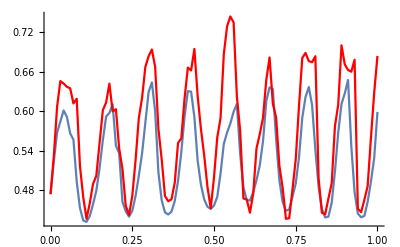

```mathematica
Show[%48,%49,PlotRange->All]
```

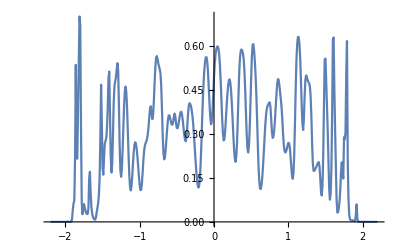

```mathematica
Show[ListLinePlot[Table[{ω,TRA[ω,5,2,1]},{ω,Range[-2.2,2.2,0.01]}]]]
```

```mathematica
ListLinePlot[Table[{ω,TRA[ω,5,4,1]},{ω,Range[-2.2,2.2,0.01]}],PlotStyle->Red]
```

```mathematica
Join[Join[Join[Table[{30+i,51-i},{i,Range[1,10,1]}],Table[{51-i,30+i},{i,Range[1,10,1]}]],Join[Table[{i,21-i},{i,Range[1,10,1]}],Table[{21-i,i},{i,Range[1,10,1]}]],Join[Table[{10+i,31-i},{i,Range[1,10,1]}],Table[{31-i,10+i},{i,Range[1,10,1]}]],Join[Table[{20+i,41-i},{i,Range[1,10,1]}],Table[{41-i,20+i},{i,Range[1,10,1]}]]],Join[Table[{30+i,51-i},{i,Range[1,10,1]}],Table[{51-i,30+i},{i,Range[1,10,1]}]],Join[Table[{40+i,61-i},{i,Range[1,10,1]}],Table[{61-i,40+i},{i,Range[1,10,1]}]],
Join[Table[{50+i,71-i},{i,Range[1,10,1]}],Table[{71-i,50+i},{i,Range[1,10,1]}]],Join[Table[{60+i,81-i},{i,Range[1,10,1]}],Table[{81-i,60+i},{i,Range[1,10,1]}]],
Join[Table[{70+i,91-i},{i,Range[1,10,1]}],Table[{91-i,70+i},{i,Range[1,10,1]}]],Join[Table[{80+i,101-i},{i,Range[1,10,1]}],Table[{101-i,80+i},{i,Range[1,10,1]}]]]
```

Range::range: Range specification in Range[2,m,1] does not have appropriate bounds.

Table::iterb: Iterator {i,Range[2,m,1]} does not have appropriate bounds.

Range::range: Range specification in Range[1,m,1] does not have appropriate bounds.

Table::iterb: Iterator {i,Range[1,m,1]} does not have appropriate bounds.

Join::heads: Heads Table and List at positions 1 and 3 are expected to be the same.

Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}],{{31,50},{32,49},{33,48},{34,47},{35,46},{36,45},{37,44},{38,43},{39,42},{40,41},{50,31},{49,32},{48,33},{47,34},{46,35},{45,36},{44,37},{43,38},{42,39},{41,40},{1,20},{2,19},{3,18},{4,17},{5,16},{6,15},{7,14},{8,13},{9,12},{10,11},{20,1},{19,2},{18,3},{17,4},{16,5},{15,6},{14,7},{13,8},{12,9},{11,10},{11,30},{12,29},{13,28},{14,27},{15,26},{16,25},{17,24},{18,23},{19,22},{20,21},{30,11},{29,12},{28,13},{27,14},{26,15},{25,16},{24,17},{23,18},{22,19},{21,20},{21,40},{22,39},{23,38},{24,37},{25,36},{26,35},{27,34},{28,33},{29,32},{30,31},{40,21},{39,22},{38,23},{37,24},{36,25},{35,26},{34,27},{33,28},{32,29},{31,30}},{{31,50},{32,49},{33,48},{34,47},{35,46},{36,45},{37,44},{38,43},{39,42},{40,41},{50,31},{49,32},{48,33},{47,34},{46,35},{45,36},{44,37},{43,38},{42,39},{41,40}},{{41,60},{42,59},{43,58},{44,57},{45,56},{46,55},{47,54},{48,53},{49,52},{50,51},{60,41},{59,42},{58,43},{57,44},{56,45},{55,46},{54,47},{53,48},{52,49},{51,50}},{{51,70},{52,69},{53,68},{54,67},{55,66},{56,65},{57,64},{58,63},{59,62},{60,61},{70,51},{69,52},{68,53},{67,54},{66,55},{65,56},{64,57},{63,58},{62,59},{61,60}},{{61,80},{62,79},{63,78},{64,77},{65,76},{66,75},{67,74},{68,73},{69,72},{70,71},{80,61},{79,62},{78,63},{77,64},{76,65},{75,66},{74,67},{73,68},{72,69},{71,70}},{{71,90},{72,89},{73,88},{74,87},{75,86},{76,85},{77,84},{78,83},{79,82},{80,81},{90,71},{89,72},{88,73},{87,74},{86,75},{85,76},{84,77},{83,78},{82,79},{81,80}},{{81,100},{82,99},{83,98},{84,97},{85,96},{86,95},{87,94},{88,93},{89,92},{90,91},{100,81},{99,82},{98,83},{97,84},{96,85},{95,86},{94,87},{93,88},{92,89},{91,90}}]

```mathematica
l[x_]:=Join[Table[{10*x+i,21+10*x-i},{i,Range[1,10,1]}],Table[{21+10*x-i,10*x+i},{i,Range[1,10,1]}]]
```

```mathematica
l[1]
```

{{11,30},{12,29},{13,28},{14,27},{15,26},{16,25},{17,24},{18,23},{19,22},{20,21},{30,11},{29,12},{28,13},{27,14},{26,15},{25,16},{24,17},{23,18},{22,19},{21,20}}

```mathematica
Table[l[x],{x,8}]
```

{{{11,30},{12,29},{13,28},{14,27},{15,26},{16,25},{17,24},{18,23},{19,22},{20,21},{30,11},{29,12},{28,13},{27,14},{26,15},{25,16},{24,17},{23,18},{22,19},{21,20}},{{21,40},{22,39},{23,38},{24,37},{25,36},{26,35},{27,34},{28,33},{29,32},{30,31},{40,21},{39,22},{38,23},{37,24},{36,25},{35,26},{34,27},{33,28},{32,29},{31,30}},{{31,50},{32,49},{33,48},{34,47},{35,46},{36,45},{37,44},{38,43},{39,42},{40,41},{50,31},{49,32},{48,33},{47,34},{46,35},{45,36},{44,37},{43,38},{42,39},{41,40}},{{41,60},{42,59},{43,58},{44,57},{45,56},{46,55},{47,54},{48,53},{49,52},{50,51},{60,41},{59,42},{58,43},{57,44},{56,45},{55,46},{54,47},{53,48},{52,49},{51,50}},{{51,70},{52,69},{53,68},{54,67},{55,66},{56,65},{57,64},{58,63},{59,62},{60,61},{70,51},{69,52},{68,53},{67,54},{66,55},{65,56},{64,57},{63,58},{62,59},{61,60}},{{61,80},{62,79},{63,78},{64,77},{65,76},{66,75},{67,74},{68,73},{69,72},{70,71},{80,61},{79,62},{78,63},{77,64},{76,65},{75,66},{74,67},{73,68},{72,69},{71,70}},{{71,90},{72,89},{73,88},{74,87},{75,86},{76,85},{77,84},{78,83},{79,82},{80,81},{90,71},{89,72},{88,73},{87,74},{86,75},{85,76},{84,77},{83,78},{82,79},{81,80}},{{81,100},{82,99},{83,98},{84,97},{85,96},{86,95},{87,94},{88,93},{89,92},{90,91},{100,81},{99,82},{98,83},{97,84},{96,85},{95,86},{94,87},{93,88},{92,89},{91,90}}}

```mathematica
Table[{20+i,41-i},{i,Range[1,10,1]}]
```

{{21,40},{22,39},{23,38},{24,37},{25,36},{26,35},{27,34},{28,33},{29,32},{30,31}}